# CEPC Higgs Precision

(Starting date: Sep. 2014)
(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
(Updated: Jul. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
(Updated: Sep. 2018 for CEPC CDR, with corrected definition of covariance matrix)
(Updated: Sep. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliuphys@umd.edu) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

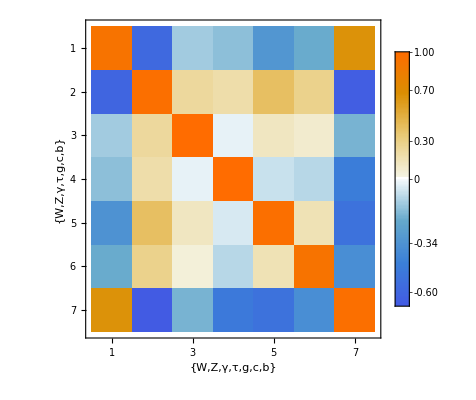

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

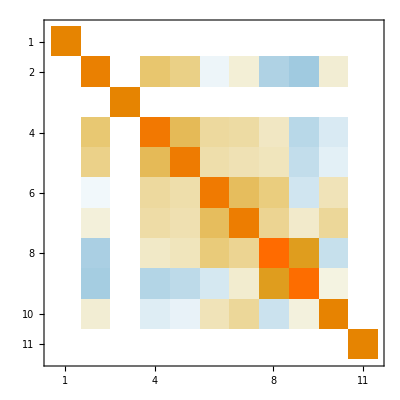

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0118029
-0.0117799)
(0.0211339
-0.0210743)
(0.0145802
-0.0144704)
(0.013066
-0.0130661)
(0.0133537
-0.0132739)
(0.00124944
-0.00125111)
(0.0361111
-0.0368686))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}}
kc | {{2.11,-2.11}}
kg | {{1.46,-1.45}}
kw | {{1.31,-1.31}}
ktau | {{1.34,-1.33}}
kz | {{0.12,-0.13}}
kgamma | {{3.61,-3.69}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(160322. | -6920.58 | -25106.6 | -54408.8 | -51941.2 | 136003. | -855.77
-6920.58 | 4057.33 | 2317.66 | 636.328 | -1205.34 | -10368.8 | 3.48455
-25106.6 | 2317.66 | 24988.2 | -788.767 | -4626.86 | -21278.4 | -16.8215
-54408.8 | 636.328 | -788.767 | 50529.1 | -670.021 | -83996.2 | 19.241
-51941.2 | -1205.34 | -4626.86 | -670.021 | 56092.4 | 20726. | -96.6801
136003. | -10368.8 | -21278.4 | -83996.2 | 20726. | 916713. | -1000.06
-855.77 | 3.48455 | -16.8215 | 19.241 | -96.6801 | -1000.06 | 855.506)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.0002 | 0.634277 | 0.891241 | 0.928746 | 0.947298 | -0.365763 | 0.345718
0.634277 | 0.999881 | 0.493384 | 0.590633 | 0.611401 | -0.138108 | 0.221453
0.891241 | 0.493384 | 1.00011 | 0.84096 | 0.858592 | -0.274619 | 0.312383
0.928746 | 0.590633 | 0.84096 | 1.0002 | 0.877789 | -0.203175 | 0.325402
0.947298 | 0.611401 | 0.858592 | 0.877789 | 1.00015 | -0.366908 | 0.330961
-0.365763 | -0.138108 | -0.274619 | -0.203175 | -0.366908 | 1. | -0.0934937
0.345718 | 0.221453 | 0.312383 | 0.325402 | 0.330961 | -0.0934937 | 0.998831)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.634252 | 0.891103 | 0.928563 | 0.947136 | -0.365727 | 0.345886
0.634252 | 1. | 0.493385 | 0.590609 | 0.611392 | -0.138116 | 0.221596
0.891103 | 0.493385 | 1. | 0.840829 | 0.85848 | -0.274604 | 0.312548
0.928563 | 0.590609 | 0.840829 | 1. | 0.877638 | -0.203155 | 0.32556
0.947136 | 0.611392 | 0.85848 | 0.877638 | 1. | -0.366881 | 0.33113
-0.365727 | -0.138116 | -0.274604 | -0.203155 | -0.366881 | 1. | -0.0935484
0.345886 | 0.221596 | 0.312548 | 0.32556 | 0.33113 | -0.0935484 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.2,1.2}} | {{0.9,0.9}}
kc | {{2.1,2.1}} | {{1.9,1.9}}
kg | {{1.5,1.4}} | {{1.1,1.1}}
kw | {{1.3,1.3}} | {{1.,1.}}
ktau | {{1.3,1.3}} | {{1.1,1.1}}
kz | {{0.1,0.1}} | {{0.1,0.1}}
kgamma | {{3.6,3.7}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.92,-0.92}}
kc | {{1.86,-1.86}}
kg | {{1.12,-1.11}}
kw | {{1.02,-1.02}}
ktau | {{1.06,-1.06}}
kz | {{0.12,-0.12}}
kgamma | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{163850.,-6765.56,-30395.9,-53159.4,-51571.5,130191.,-842.466},{-6765.56,4464.51,1672.6,694.216,-1188.21,-10629.7,4.10095},{-30395.9,1672.6,34243.3,-2763.87,-5211.36,-12872.4,-37.8527},{-53159.4,694.216,-2763.87,53263.2,-531.952,-88366.1,24.209},{-51571.5,-1188.21,-5211.36,-531.952,56566.4,19670.8,-95.21},{130191.,-10629.7,-12872.4,-88366.1,19670.8,932650.,-4108.87},{-842.466,4.10095,-37.8527,24.209,-95.21,-4108.87,3941.98}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00007 | 0.568505 | 0.869305 | 0.884889 | 0.916009 | -0.305686 | 0.11436
0.568505 | 0.99986 | 0.446227 | 0.506599 | 0.536605 | -0.0609252 | 0.0729729
0.869305 | 0.446227 | 1.00004 | 0.791764 | 0.816927 | -0.228556 | 0.104253
0.884889 | 0.506599 | 0.791764 | 1.00007 | 0.807764 | -0.0926284 | 0.114409
0.916009 | 0.536605 | 0.816927 | 0.807764 | 1.00004 | -0.306455 | 0.105363
-0.305686 | -0.0609252 | -0.228556 | -0.0926284 | -0.306455 | 1. | 0.0352106
0.11436 | 0.0729729 | 0.104253 | 0.114409 | 0.105363 | 0.0352106 | 0.999979)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.568526 | 0.86926 | 0.884826 | 0.915959 | -0.305676 | 0.114357
0.568526 | 1. | 0.44625 | 0.506615 | 0.536632 | -0.0609295 | 0.0729788
0.86926 | 0.44625 | 1. | 0.791719 | 0.816895 | -0.228551 | 0.104252
0.884826 | 0.506615 | 0.791719 | 1. | 0.807718 | -0.0926249 | 0.114405
0.915959 | 0.536632 | 0.816895 | 0.807718 | 1. | -0.306449 | 0.105362
-0.305676 | -0.0609295 | -0.228551 | -0.0926249 | -0.306449 | 1. | 0.035211
0.114357 | 0.0729788 | 0.104252 | 0.114405 | 0.105362 | 0.035211 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0133936
-0.0133223)
(0.0226142
-0.0225025)
(0.0160061
-0.015846)
(0.01446
-0.0144269)
(0.0149912
-0.0148566)
(0.00249688
-0.00250313)
(0.0384763
-0.0392703)
(0.0821896
-0.0885931)
(0.00165002
-0.00165)
(0.029582
-0.0289054))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.03}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651845 | 0.90324 | 0.933432 | 0.955591 | 0.192915 | 0.366548 | 0.155284 | 0. | 0.981766
0.651845 | 0.999874 | 0.525308 | 0.614637 | 0.632549 | 0.115783 | 0.242468 | 0.102719 | 0. | 0.64735
0.90324 | 0.525308 | 1.0001 | 0.857995 | 0.875629 | 0.162086 | 0.335991 | 0.142339 | 0. | 0.897332
0.933432 | 0.614637 | 0.857995 | 1.0002 | 0.890389 | 0.181259 | 0.347828 | 0.147354 | 0. | 0.931308
0.955591 | 0.632549 | 0.875629 | 0.890389 | 1.00012 | 0.172568 | 0.353482 | 0.149749 | 0. | 0.944404
0.192915 | 0.115783 | 0.162086 | 0.181259 | 0.172568 | 1.00013 | 0.0679164 | 0.028772 | 0. | 0.351261
0.366548 | 0.242468 | 0.335991 | 0.347828 | 0.353482 | 0.0679164 | 0.998815 | 0.0574918 | 0. | 0.362869
0.155284 | 0.102719 | 0.142339 | 0.147354 | 0.149749 | 0.028772 | 0.0574918 | 0.992492 | 0. | 0.153725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999975 | 0.
0.981766 | 0.64735 | 0.897332 | 0.931308 | 0.944404 | 0.351261 | 0.362869 | 0.153725 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0104943
-0.0104332)
(0.0197317
-0.0196929)
(0.0123105
-0.0122082)
(0.0111677
-0.0111372)
(0.0119986
-0.0118974)
(0.00249688
-0.00250313)
(0.016438
-0.0164584)
(0.0491767
-0.0498656)
(0.00165
-0.00165)
(0.0236218
-0.023157))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.34,-1.33}} | {{1.05,-1.04}}
kt | {{2.26,-2.25}} | {{1.97,-1.97}}
kg | {{1.6,-1.58}} | {{1.23,-1.22}}
kw | {{1.45,-1.44}} | {{1.12,-1.11}}
ktau | {{1.5,-1.49}} | {{1.2,-1.19}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.85,-3.93}} | {{1.64,-1.65}}
kmu | {{8.22,-8.86}} | {{4.92,-4.99}}
brinv | {{0.17,-0.16}} | {{0.17,-0.17}}
ktotal | {{2.96,-2.89}} | {{2.36,-2.32}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.34,-1.33}} | {{1.05,-1.04}}
kt | {{2.26,-2.25}} | {{1.97,-1.97}}
kg | {{1.6,-1.58}} | {{1.23,-1.22}}
kw | {{1.45,-1.44}} | {{1.12,-1.11}}
ktau | {{1.5,-1.49}} | {{1.2,-1.19}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.85,-3.93}} | {{1.64,-1.65}}
kmu | {{8.22,-8.86}} | {{4.92,-4.99}}
brinv | {{0.17,-0.16}} | {{0.17,-0.17}}
ktotal | {{2.96,-2.89}} | {{2.36,-2.32}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 1.
kt | 2.2 | 1.9
kg | 1.5 | 1.2
kw | 1.4 | 1.1
ktau | 1.4 | 1.2
kz | 0.2 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 2.8 | 2.3)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00004 | 0.587305 | 0.88845 | 0.89504 | 0.931421 | 0.242999 | 0.170569 | 0.0798631 | 0. | 0.972108
0.587305 | 0.99985 | 0.480479 | 0.534927 | 0.561191 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.88845 | 0.480479 | 1.00002 | 0.817184 | 0.844922 | 0.207507 | 0.153268 | 0.0720641 | 0. | 0.879635
0.89504 | 0.534927 | 0.817184 | 1.00007 | 0.831242 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931421 | 0.561191 | 0.844922 | 0.831242 | 1.00002 | 0.213239 | 0.15925 | 0.0749428 | 0. | 0.915308
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.050151 | 0. | 0.43334
0.170569 | 0.100895 | 0.153268 | 0.157685 | 0.15925 | 0.153555 | 0.99997 | 0.0174489 | 0. | 0.191394
0.0798631 | 0.0475803 | 0.0720641 | 0.0736481 | 0.0749428 | 0.050151 | 0.0174489 | 0.999779 | 0. | 0.0851412
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999975 | 0.
0.972108 | 0.581922 | 0.879635 | 0.894973 | 0.915308 | 0.43334 | 0.191394 | 0.0851412 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999925,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.999988,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

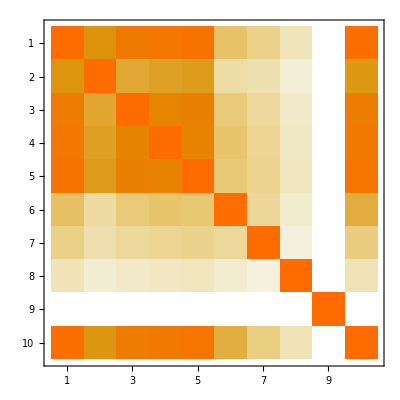

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## CDR (width subchannel ZZ)

```mathematica
(*It is triky now to define subchannel fit; there are two approaches, which might cause confusion, I list them here*)
(*1: freeze all the other measurements/parameters, techinically means we set the precision to infinity for iirelevant channels; this will first improve a given cross section measurement, then we combine. In other words, the fit input precision will change for the relevant channels. It then will be hard to combine different channels as they will correspond to different degree of freedoms.*)
(*2: use the same input precision but remove the correlation entries with irrelavant ones, then calculate. This avoids the problem above. I will take the second approach.*)
```

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
inputcorrelationsoriginal=inputcorrelations;
```

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]ᵀ)/100]
```

{{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,-0.2,0.2,0.002}]
```

{{-0.2,22.9286},{-0.198,22.3667},{-0.196,21.8142},{-0.194,21.2712},{-0.192,20.7376},{-0.19,20.2131},{-0.188,19.6978},{-0.186,19.1914},{-0.184,18.6939},{-0.182,18.2052},{-0.18,17.7252},{-0.178,17.2537},{-0.176,16.7907},{-0.174,16.3361},{-0.172,15.8898},{-0.17,15.4516},{-0.168,15.0215},{-0.166,14.5993},{-0.164,14.1851},{-0.162,13.7786},{-0.16,13.3799},{-0.158,12.9887},{-0.156,12.6051},{-0.154,12.2289},{-0.152,11.86},{-0.15,11.4984},{-0.148,11.1439},{-0.146,10.7966},{-0.144,10.4562},{-0.142,10.1228},{-0.14,9.79615},{-0.138,9.4763},{-0.136,9.16313},{-0.134,8.85655},{-0.132,8.5565},{-0.13,8.2629},{-0.128,7.97566},{-0.126,7.69473},{-0.124,7.42001},{-0.122,7.15145},{-0.12,6.88896},{-0.118,6.63248},{-0.116,6.38194},{-0.114,6.13726},{-0.112,5.89839},{-0.11,5.66525},{-0.108,5.43777},{-0.106,5.2159},{-0.104,4.99956},{-0.102,4.78869},{-0.1,4.58323},{-0.098,4.38311},{-0.096,4.18828},{-0.094,3.99866},{-0.092,3.81421},{-0.09,3.63486},{-0.088,3.46055},{-0.086,3.29123},{-0.084,3.12683},{-0.082,2.9673},{-0.08,2.81258},{-0.078,2.66263},{-0.076,2.51737},{-0.074,2.37676},{-0.072,2.24075},{-0.07,2.10928},{-0.068,1.9823},{-0.066,1.85976},{-0.064,1.7416},{-0.062,1.62778},{-0.06,1.51825},{-0.058,1.41295},{-0.056,1.31184},{-0.054,1.21487},{-0.052,1.12199},{-0.05,1.03316},{-0.048,0.948325},{-0.046,0.867444},{-0.044,0.790471},{-0.042,0.71736},{-0.04,0.648066},{-0.038,0.582547},{-0.036,0.520759},{-0.034,0.462659},{-0.032,0.408204},{-0.03,0.357354},{-0.028,0.310065},{-0.026,0.266298},{-0.024,0.226012},{-0.022,0.189167},{-0.02,0.155723},{-0.018,0.125642},{-0.016,0.0988852},{-0.014,0.0754138},{-0.012,0.0551905},{-0.01,0.0381779},{-0.008,0.0243391},{-0.006,0.0136378},{-0.004,0.00603783},{-0.002,0.00150364},{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483},{0.102,3.22928},{0.104,3.34538},{0.106,3.46311},{0.108,3.58246},{0.11,3.7034},{0.112,3.82591},{0.114,3.94998},{0.116,4.07559},{0.118,4.20272},{0.12,4.33134},{0.122,4.46145},{0.124,4.59303},{0.126,4.72605},{0.128,4.86051},{0.13,4.99638},{0.132,5.13364},{0.134,5.27228},{0.136,5.41229},{0.138,5.55364},{0.14,5.69633},{0.142,5.84033},{0.144,5.98562},{0.146,6.1322},{0.148,6.28005},{0.15,6.42914},{0.152,6.57948},{0.154,6.73103},{0.156,6.88379},{0.158,7.03775},{0.16,7.19288},{0.162,7.34917},{0.164,7.50661},{0.166,7.66518},{0.168,7.82488},{0.17,7.98568},{0.172,8.14757},{0.174,8.31054},{0.176,8.47458},{0.178,8.63967},{0.18,8.80579},{0.182,8.97295},{0.184,9.14111},{0.186,9.31028},{0.188,9.48044},{0.19,9.65157},{0.192,9.82366},{0.194,9.9967},{0.196,10.1707},{0.198,10.3456},{0.2,10.5214}}

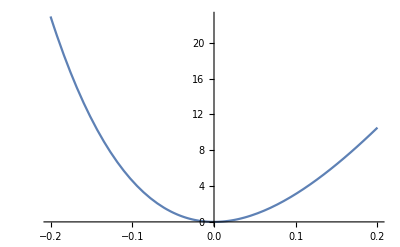

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.2,0.2}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

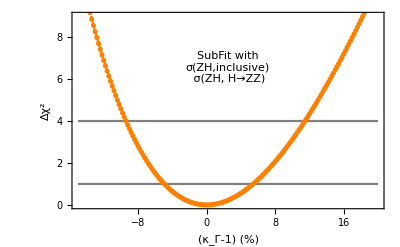

{{x→0.0543855}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.15*100,0.2*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Orange,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata,PlotStyle->Orange],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→ZZ)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

## CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]ᵀ)/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.00009 | 0. | 0. | 0. | -0.00969845 | 5.10855×10^-6 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.00969845 | 0. | 0. | 0. | 1.30284 | 0.628015 | 0. | 0.
0. | 0. | 0. | 5.10855×10^-6 | 0. | 0. | 0. | 0.628015 | 1.30275 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1448.37 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2+13650.7 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+138414. (-1+(kb^2 kz^2)/ktotal)^2+0.0347625 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)-645.135 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10413.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.67745},{-0.098,8.32755},{-0.096,7.9851},{-0.094,7.65009},{-0.092,7.3225},{-0.09,7.00231},{-0.088,6.6895},{-0.086,6.38407},{-0.084,6.086},{-0.082,5.79526},{-0.08,5.51185},{-0.078,5.23574},{-0.076,4.96693},{-0.074,4.70539},{-0.072,4.45112},{-0.07,4.20409},{-0.068,3.96428},{-0.066,3.7317},{-0.064,3.5063},{-0.062,3.28809},{-0.06,3.07705},{-0.058,2.87315},{-0.056,2.67639},{-0.054,2.48675},{-0.052,2.3042},{-0.05,2.12875},{-0.048,1.96037},{-0.046,1.79904},{-0.044,1.64475},{-0.042,1.49749},{-0.04,1.35724},{-0.038,1.22398},{-0.036,1.09769},{-0.034,0.978371},{-0.032,0.865995},{-0.03,0.76055},{-0.028,0.662019},{-0.026,0.570388},{-0.024,0.485642},{-0.022,0.407763},{-0.02,0.336738},{-0.018,0.27255},{-0.016,0.215184},{-0.014,0.164625},{-0.012,0.120857},{-0.01,0.0838643},{-0.008,0.0536322},{-0.006,0.0301451},{-0.004,0.0133876},{-0.002,0.00334435},{0.,1.00593×10^-21},{0.002,0.00333925},{0.004,0.0133468},{0.006,0.0300074},{0.008,0.0533057},{0.01,0.0832266},{0.012,0.119755},{0.014,0.162875},{0.016,0.212572},{0.018,0.268831},{0.02,0.331637},{0.022,0.400973},{0.024,0.476827},{0.026,0.559181},{0.028,0.648022},{0.03,0.743334},{0.032,0.845101},{0.034,0.95331},{0.036,1.06795},{0.038,1.18899},{0.04,1.31643},{0.042,1.45026},{0.044,1.59045},{0.046,1.73699},{0.048,1.88986},{0.05,2.04906},{0.052,2.21457},{0.054,2.38637},{0.056,2.56444},{0.058,2.74878},{0.06,2.93936},{0.062,3.13618},{0.064,3.33922},{0.066,3.54846},{0.068,3.76388},{0.07,3.98549},{0.072,4.21325},{0.074,4.44715},{0.076,4.68719},{0.078,4.93334},{0.08,5.1856},{0.082,5.44394},{0.084,5.70835},{0.086,5.97882},{0.088,6.25533},{0.09,6.53788},{0.092,6.82643},{0.094,7.12099},{0.096,7.42153},{0.098,7.72805},{0.1,8.04052}}

```mathematica
tempdata={{-0.1,8.677450891966563},{-0.098,8.32755196261379},{-0.096,7.985104085000047},{-0.094,7.65009132190818},{-0.092,7.322497744092595},{-0.09000000000000001,7.00230743052874},{-0.08800000000000001,6.689504468660578},{-0.08600000000000001,6.384072954645076},{-0.084,6.085996993594568},{-0.082,5.795260699816512},{-0.08,5.5118481970510524},{-0.07800000000000001,5.2357436187057855},{-0.07600000000000001,4.966931108088384},{-0.07400000000000001,4.705394818636952},{-0.07200000000000001,4.451118914147368},{-0.07,4.204087568999234},{-0.068,3.9642849683785095},{-0.066,3.731695308498466},{-0.064,3.5063027968179235},{-0.062000000000000006,3.288091652257446},{-0.060000000000000005,3.0770461054129132},{-0.058,2.8731503987672258},{-0.05600000000000001,2.6763887868992593},{-0.054000000000000006,2.4867455366909117},{-0.052000000000000005,2.3042049275318166},{-0.05,2.128751251521669},{-0.048,1.9603688136703976},{-0.046000000000000006,1.7990419320963464},{-0.044000000000000004,1.6447549382218103},{-0.042,1.497492176966834},{-0.04000000000000001,1.3572380069406136},{-0.038000000000000006,1.2239768006306484},{-0.036000000000000004,1.0976929445899921},{-0.034,0.9783708396221834},{-0.032,0.8659949009641101},{-0.03,0.7605495584667874},{-0.027999999999999997,0.662019256774069},{-0.02600000000000001,0.5703884554991236},{-0.024000000000000007,0.4856416293990754},{-0.022000000000000006,0.40776326854740963},{-0.020000000000000004,0.33673787850437903},{-0.018000000000000002,0.2725499804854658},{-0.016,0.2151841115277067},{-0.013999999999999999,0.1646248246541206},{-0.01200000000000001,0.12085668903607161},{-0.010000000000000009,0.08386429015371458},{-0.008000000000000007,0.05363222995443828},{-0.006000000000000005,0.03014512700938449},{-0.0040000000000000036,0.013387616668033502},{-0.0020000000000000018,0.0033443512108399156},{0.,1.0059323527535169*^-21},{0.0020000000000000018,0.0033392496282892824},{0.0040000000000000036,0.013346804066036977},{0.0059999999999999915,0.030007384806224828},{0.007999999999999993,0.05330573100773261},{0.009999999999999995,0.08322659963673108},{0.011999999999999997,0.11975476560626021},{0.013999999999999999,0.16287502191397366},{0.016,0.21257217977809145},{0.018000000000000002,0.26883106877155705},{0.01999999999999999,0.3316365369544218},{0.021999999999999992,0.40097345100442205},{0.023999999999999994,0.47682669634590685},{0.025999999999999995,0.5591811772768627},{0.027999999999999997,0.6480218170944044},{0.03,0.7433335582183932},{0.032,0.8451013623134185},{0.034,0.953310210409061},{0.036000000000000004,1.0679451030185831},{0.038000000000000006,1.1889910602557783},{0.04000000000000001,1.3164331219503247},{0.04200000000000001,1.4502563477614159},{0.04400000000000001,1.590445817289781},{0.045999999999999985,1.7369866301881352},{0.04799999999999999,1.8898639062699338},{0.04999999999999999,2.0490627856166266},{0.05199999999999999,2.214568428683308},{0.05399999999999999,2.3863660164027656},{0.055999999999999994,2.5644407502880844},{0.057999999999999996,2.7487778525334825},{0.06,2.939362566113899},{0.062,3.136180154882916},{0.064,3.339215903669179},{0.066,3.5484551183712343},{0.068,3.7638831260511996},{0.07,3.985485275026532},{0.07200000000000001,4.213246934960835},{0.07400000000000001,4.447153496952563},{0.07599999999999998,4.6871903736230704},{0.07799999999999999,4.933342999202642},{0.07999999999999999,5.18559682961534},{0.08199999999999999,5.443937342562357},{0.08399999999999999,5.708350037604303},{0.086,5.97882043624158},{0.088,6.255334081993829},{0.09,6.537876540477849},{0.092,6.826433399484211},{0.094,7.120990269052509},{0.096,7.421532781545281},{0.098,7.728046591720733},{0.1,8.040517376804022}};
```

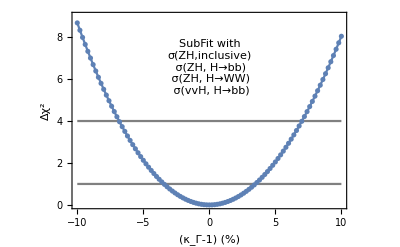

{{x→0.0348282}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.1*100,0.1*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Automatic,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→bb)\n σ(ZH, H→WW)\n σ(vvH, H→bb)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

```mathematica
1/Sqrt[1/3.5^2+1/5.4^2]
```

2.93704

## Tests

```mathematica
chisquare=(x^2/z)^2/dx^2+(y^2/z)^2/dy^2+x^4/dxp^2
```

x^4/dxp^2+x^4/(dx^2 z^2)+y^4/(dy^2 z^2)

```mathematica
{{D[chisquare,x,x],D[chisquare,x,y],D[chisquare,x,z]},
{D[chisquare,y,x],D[chisquare,y,y],D[chisquare,y,z]},
{D[chisquare,z,x],D[chisquare,z,y],D[chisquare,z,z]}}/2/.{x->1,y->1,z->1};
%//MatrixForm
```

(1/2 (12/dx^2+12/dxp^2) | 0 | -4/dx^2
0 | 6/dy^2 | -4/dy^2
-4/dx^2 | -4/dy^2 | 1/2 (6/dx^2+6/dy^2))

```mathematica
Inverse[%658]//Simplify;
%//MatrixForm
```

((dx^2 dxp^2 (dx^2+9 dy^2))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (dy^2 (9 dx^4+dxp^2 dy^2+9 dx^2 (dxp^2+dy^2)))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (3 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)))

## 7-kappa deriving width for a random request from a senior member (really wasting time)

```mathematica
NSolve[kh[kz,kw,kg,kgamma,kb,kt,ktau]kappah==1,kb]
```

{{kb→-1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)},{kb→1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)}}

```mathematica
Module[{kappah},kappah=0.95;NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}]]
```

{4.82534,{kz→0.999106,kg→1.02916,kgamma→1.02834,kw→1.0274,kt→1.03051,ktau→1.02792}}

```mathematica
widthdata70=Table[{kappah,NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,4.82534},{0.955,3.87901},{0.96,3.04191},{0.965,2.31162},{0.97,1.68578},{0.975,1.16209},{0.98,0.738316},{0.985,0.412298},{0.99,0.181927},{0.995,0.0451574},{1.,8.65073×10^-11},{1.005,0.0445222},{1.01,0.176845},{1.015,0.395143},{1.02,0.69764},{1.025,1.08261},{1.03,1.54838},{1.035,2.0933},{1.04,2.71581},{1.045,3.41435},{1.05,4.18742}}

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,{x,1.02}]
```

NSolve::ivar: 1.02 is not a valid variable.

NSolve[InterpolatingFunction[…][1+x]==1,{x,1.02}]

```mathematica
widthdata70L=Table[{kappah,NMinimize[{chisquarecepcL[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,8.13819},{0.955,6.54393},{0.96,5.13311},{0.965,3.90178},{0.97,2.84613},{0.975,1.96245},{0.98,1.2471},{0.985,0.696577},{0.99,0.307432},{0.995,0.0763258},{1.,1.32684×10^-13},{1.005,0.0752819},{1.01,0.29908},{1.015,0.668383},{1.02,1.18026},{1.025,1.83184},{1.03,2.62034},{1.035,3.54305},{1.04,4.59732},{1.045,5.78057},{1.05,7.09028}}

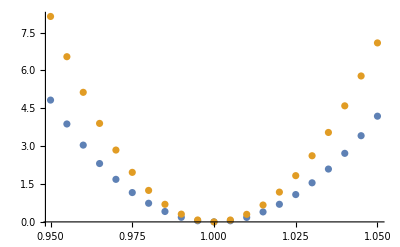

```mathematica
ListPlot[{widthdata70,widthdata70L}]
```

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,x]
NSolve[Interpolation[widthdata70L][1+x]==1,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0232213}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0179354}}

```mathematica
FindRoot[Interpolation[widthdata70][1+x]==1,{x,0}]
FindRoot[Interpolation[widthdata70L][1+x]==1,{x,0}]
```

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.024011}

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.0183896}